```mathematica
QEA - Differential Equations Reading-Part II
```

```mathematica
SetDirectory@NotebookDirectory[];
<<"../General.m"
```

## Heating Stuff Up Cooling Stuff Down

```mathematica
With[{context="heatingstuffupcoolingstuffdown`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### First we need to find the general differential equation for our system. We have calculated h to be .0364 by equation our power flows when the temperature no longer changes (such that Cp * DT/dt = 0. We were able to find this value with our experimental data.

```mathematica
With[{V=9,R=50,Troom=26.8,h=0.0364},
de={T'[t]==1/Cp(V^2/R-h(T[t]- Troom))};
initialConditions={T[0]==Troom};

sol=DSolveValue[Join[de,initialConditions],T[t],t]
]
```

71.3055 ⅇ^(-(0.0364 t)/Cp) (-0.624152+1. ⅇ^((0.0364 t)/Cp))

### Next, we want to find Cp with our data. Let’s import it and plot it to make sure it is what we expect. We also have to center the x axis at zero and start the y axis in terms of Celsius.

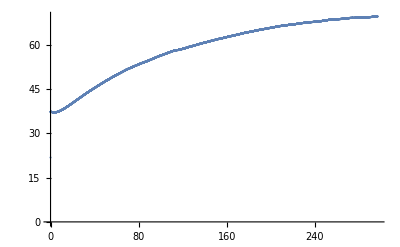

```mathematica
data=Import["temprun.csv","CSV"];
x=Transpose[data][[1]]-Min[Transpose[data][[1]]];
y=Transpose[data][[2]]*100;
dataPlot=ListPlot[Transpose@{x,y}]
```

### To get Cp, we have to fit it to our data. We will use our general differential equation as a base to find the correct fit. Although unnecessary, the guess of 10 makes sure that Mathematica finds a Cp close to 10.

```mathematica
Clear[cp, Cp]
cp =FindFit[Transpose@{x,y},sol,{{Cp, 10}},t]
```

{Cp→3.22476}

### Now plot the DE and the data on the same plot to see how accurate we are. Seems to be pretty good. The reason why the graphs start at the different places is because we had heated the resistor a little before we started taking data.

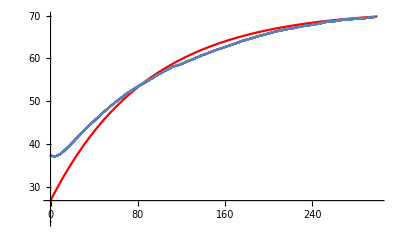

```mathematica
DEPlot=Plot[sol/.cp,{t,0,300},PlotRange->All,PlotStyle->Red];
Show[DEPlot,dataPlot]
```

### Finally a vector plot from temp 0 to 100.

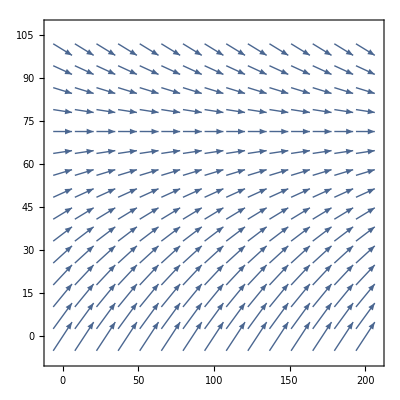

```mathematica
With[{V=9,R=50,Troom=26.8,h=0.0364,Cp=3.2247579045628525},
de=1/Cp(V^2/R-h(T- Troom));
VectorPlot[{1,de},{t,0,200},{T,0,100}]
]
```

```mathematica
With[{context="heatingstuffupcoolingstuffdown`"},If[Context[]==context,End[],"Not in context"]]
```

heatingstuffupcoolingstuffdown`

```mathematica
exportNotebookPDF[]
```

/home/nathan/olin/fall2016/qEAFall2016Homework/attitudeControl/differentialEquations/differentialEquationsPart2.pdf